## Initialisation stuff

```mathematica
Needs["QDENSITY`Qdensity`"];
packageDir =FileNameJoin[{ NotebookDirectory[],"QSIM"}];
Needs["QSIM`noise`",FileNameJoin[{packageDir,"QSIM_noise.m"}]]
```

```mathematica
?QDENSITY`Qdensity`*
```

```mathematica
ExpmFidelity[Op1_,Op2_]:=Fidelity[Op1,Op2]^2;
CombineErrors[errorTable_]:=Module[{x,probNone},probNone=Times@@((1-#)&/@errorTable);
Total[Table[probNone errorTable[[ii]]/(1-errorTable[[ii]]),{ii,1,Length[errorTable]}]]](*for small probabilities, these depolarizing channels just add up.*)
PZ[i_]:=Switch[i,0,Subscript[𝒫, 0],1,Subscript[𝒫, 1]];
projectors={PX,PY,PZ};
KP[r__]:=KroneckerProduct[r];
phi0={{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}};
id =𝕀;
bellState[i_]:=ArrayFlatten[Outer[Times,PauliMatrix[i],PauliMatrix[0]]].phi0.ArrayFlatten[Outer[Times,PauliMatrix[i],PauliMatrix[0]]];
```

#### Single qubit gates

```mathematica
(*Definition of single spin rotations using the qdensity package
Nomenclature:  r followed by a capital letter --> rotation by π around the axis specified by the letter.
			r followed by a lower case letter: rotation by π/2 around the axis specified by that letter
The rotation direction is given by the appended letter m or p*)

{rxp,rXp,ryp,rYp,rzp,rZp}=Table[MatrixExp[-ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))],{j,1,6}];
{rxm,rXm,rym,rYm,rzm,rZm}=Table[MatrixExp[ⅈ*Subscript[σ, Floor[j/2-0.01]+1]*π/(2*(1+Mod[j,2]))],{j,1,6}];
```

#### Data functions

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
findFileInDataDir[string_,dataDir_,daysPreviousToSearch_:365]:=Module[{filenames,daysPrevious},daysPrevious=0;While[(daysPrevious<daysPreviousToSearch) &&( Length[filenames]==0),filenames=Select[FileNames["*"<>string<>"*",FileNameJoin[{dataDir,DateString[AbsoluteTime[]-86400 daysPrevious,{"Year","Month","Day"}]}]],DirectoryQ];daysPrevious++;];Return[filenames]]

GetDirectoryNameContaining::notunique="File not unique";
GetDirectoryNameContaining::nofile="No matching file found";
GetDirectoryNameContaining[string_,dir_:NotebookDirectory[],searchDataDir_:True]:=Module[{filenames},If[searchDataDir==False,filenames=Select[FileNames["*"<>string<>"*",dir],DirectoryQ];,filenames=findFileInDataDir[string,dir]];
Which[Length[filenames]==1,Return[filenames[[1]]],Length[filenames]==0,Message[GetDirectoryNameContaining::nofile];Return[$Failed],Length[filenames]>0,Message[GetDirectoryNameContaining::notunique];Return[$Failed]]]

GetCorrelationFile[string_,dir_:NotebookDirectory[],exactDir_:False,twoDsweep_:False,corrFileName_:"correlations.h5"]:=Module[{Corrs},Corrs=
Import[FileNameJoin[{If[exactDir,dir,GetDirectoryNameContaining[string,dir]],corrFileName}],{"Datasets",If[twoDsweep,{"/sweep_pts1","/sweep_pts2","/correlations","/correlations_u","/norm_correlators","/norm_correlators_u","/counts_per_pt","tail_counts","tail_counts_u"},{"/sweep_pts","/correlations","/correlations_u","/norm_correlators","/norm_correlators_u","/counts_per_pt","tail_counts","tail_counts_u"}]}];
If[Not[twoDsweep],Corrs=Insert[Corrs,{1},1];
(Corrs[[#]]={Corrs[[#]]})&/@{3,4,5,6,7};];
Return[Corrs];]

getFileCorrs[fileNameArray_,corrFileName_:"correlations.h5"]:=Module[{Corrs},Corrs={};
(AppendTo[Corrs,GetCorrelationFile["",FileNameJoin[{BaseDirString,#}],True,False,corrFileName]])&/@fileNameArray;
Return[Corrs]];
```

```mathematica
GetAdwinVarFile[string_,dir_:NotebookDirectory[],exactDir_:False,corrFileName_:"adwin_vars.h5"]:=
Import[FileNameJoin[{If[exactDir,dir,GetDirectoryNameContaining[string,dir]],corrFileName}],{"Datasets",{"/DD_repetitions_centers","/DD_repetitions","/time_in_cr_and_comm_centers","/time_in_cr_and_comm"}}]

getFileAdwinVars[fileNameArray_]:=Module[{vars},vars={};
(AppendTo[vars,GetAdwinVarFile["",FileNameJoin[{BaseDirString,#}],True]])&/@fileNameArray;
Return[vars]];
```

```mathematica
FidFromData[corrs_]:=((1+Total[Abs[#]])/4&/@#)&/@corrs;
FidErrorFromData[corrsError_]:=((Sqrt[Total[#^2]]/4)&/@#)&/@corrsError;

CreateDataFidelityList[LDEAttempts_,fileCorrs_]:=Transpose@({{#[[1]],#[[2]]},ErrorBar[#[[3]]]}&/@Transpose@{{#[[1]],#[[1]]},FidFromData[#[[2]][[3]]][[1]],FidErrorFromData[#[[2]][[4]]][[1]]}&/@Transpose[{LDEAttempts,fileCorrs}])
CreateDataAvgFidelityList[LDEAttempts_,fileCorrs_]:=({{#[[1]],Mean[FidFromData[#[[2]][[3]]][[1]]]},ErrorBar[Sqrt[Total[(FidErrorFromData[#[[2]][[4]]][[1]])^2]]/2]}&/@Transpose[{LDEAttempts,fileCorrs}])
```

```mathematica
GetMsmtFilenameContaining::notunique="File not unique";
GetMsmtFilenameContaining::nofile="No matching file found";
GetMsmtFilenameContaining[string_,dir_:NotebookDirectory[]]:=Module[{filenames,dirname},dirname=GetDirectoryNameContaining[string,dir];
Return[FileNameJoin[{dirname,FileNameSplit[dirname][[-1]]<>".hdf5"}]];]

GetAdwinGroup[filename_]:=Module[{groups,group,x},
groups=StringSplit[Import[filename,"Groups"],"/"];
For[x=1,x<=Length[groups],x++,group=groups[[x]];(Which[Length[group]==0,Null,group[[-1]]=="adwindata",Return["/"<>StringJoin[Riffle[group,"/"]]]])];
Return[$Failed]];

GetAdwinData[filename_,arrayname_]:=If[$VersionNumber≥10,Import[filename,{"Datasets",GetAdwinGroup[filename]<>"/"<>arrayname}],Import[filename,{"Datasets",GetAdwinGroup[filename]<>"/"<>arrayname}]];

GetPQData[filename_,arrayname_]:=Import[filename,arrayname];

GetMsmtAttribute[filename_,attribute_]:=
If[$VersionNumber≥10,(attribute)/.(Import[filename,{"Attributes",GetAdwinGroup[filename]}]),attribute/.((GetAdwinGroup[filename])/.Import[filename,{"Attributes"}])]

GetMsmtAttributeNames[filename_]:=
Keys[Import[filename,{"Attributes",GetAdwinGroup[filename]}]];
```

## Model

Parameters that define the raw state (generated by a single photon click): 

vis - the visibility of the photons
fz  - determined by initialization error, MW pulse infidelity and spin flip probability  
r  - the proportion of the state in the unentangled ‘11’ state

The r value depends on: 
pDetect - detection efficiency
theta  - the initial rotation of the state of the qubits: Cos[theta]|0> + Sin[theta]|1>
PDC - dark count prob per detector

the function rawState[fid_,pLoss_] generates a density matrix of the entangled state generated after a single detector click

```mathematica
rValue[theta_,pDetect1_,pDetect2_,pDC_]:=Module[{p00,p01,p10,p11,pd1,pd2},
pd1 = pDetect1;
pd2 = pDetect2;

p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd2+ 2*pDC*(1-pDC)*(1-pd2));
p10 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd1+ 2*pDC*(1-pDC)*(1-pd1));
p11 = Sin[theta]^4 *((1-pDC)^2*(pd1*(1-pd2)+pd2*(1-pd1)) + 2*(1-pDC)*pDC*(1-pd1)*(1-pd2));

{p00,p01,p10,p11}/(p00+p01+p10+p11)
]
```

```mathematica
rValueBK[theta_,pDetect1_,pDetect2_,pDC_]:=Module[{p00,p01,p10,p11,pd1,pd2,p00BK,p10BK},
pd1 = pDetect1;
pd2 = pDetect2;

p00 = 2*Cos[theta]^4*pDC*(1-pDC);
p01 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd2+ 2*pDC*(1-pDC)*(1-pd2));
p10 = (Sin[theta])^2(Cos[theta])^2*((1-pDC)^2 * pd1+ 2*pDC*(1-pDC)*(1-pd1));
p11 = Sin[theta]^4 *((1-pDC)^2*(pd1*(1-pd2)+pd2*(1-pd1)) + 2*(1-pDC)*pDC*(1-pd1)*(1-pd2));

p00BK=p11 p00;
p10BK=p01 p10;
{p00BK,p10BK,p10BK,p00BK}/(2p00BK+2p10BK)
]
```

#### Raw state generation

```mathematica
rawState[vis_,fz_,rValue_,RndOpticalPhase_]:=Chop[rValue[[1]]*KP[Subscript[𝒫, 1],Subscript[𝒫, 1]]+{{(1-fz)(rValue[[2]]+rValue[[3]])/2,0,0,0},{0,rValue[[2]]*fz,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[ⅈ*RndOpticalPhase],0},{0,-vis*Sqrt[rValue[[2]]*rValue[[3]]]*fz*Exp[-ⅈ*RndOpticalPhase],rValue[[3]]*fz,0},{0,0,0,(1-fz)(rValue[[2]]+rValue[[3]])/2}}+rValue[[4]]*KP[Subscript[𝒫, 0],Subscript[𝒫, 0]]];
```

```mathematica
initialState[θ_]:={{Sin[θ]^2,Cos[θ] Sin[θ]},{Cos[θ] Sin[θ],Cos[θ]^2}}
productRawState[θ_]:=KP[initialState[θ],initialState[θ]];
decoheredRawState[θ_]:={{Sin[θ]^4,0,0,0},{0,Cos[θ]^2 Sin[θ]^2,0,0},{0,0,Cos[θ]^2 Sin[θ]^2,0},{0,0,0,Cos[θ]^4}}
```

```mathematica
BKState[setupParams_]:=Module[{pDoubleExcite,DM},
pDoubleExcite = setupParams["pDoubleExcite"];
DM = rawState[setupParams["vis"],setupParams["fz"],rValueBK[π/4,setupParams["pDetect1"],setupParams["pDetect2"],setupParams["pDC"]],0];
(*include phase error due to double excitation (removes all coherences)*)
DM=(1-pDoubleExcite/2)^2 DM + (1-pDoubleExcite/2)pDoubleExcite /2(KP[Subscript[σ, 3],𝕀].DM.KP[Subscript[σ, 3],𝕀]†)+(1-pDoubleExcite/2)pDoubleExcite/2 (KP[𝕀,Subscript[σ, 3]].DM.KP[𝕀,Subscript[σ, 3]]†) + (pDoubleExcite/2)^2(KP[Subscript[σ, 3],Subscript[σ, 3]].DM.KP[Subscript[σ, 3],Subscript[σ, 3]]†);
DM=(1-pDoubleExcite/2)^2 DM + (1-pDoubleExcite/2)pDoubleExcite /2(KP[Subscript[σ, 3],𝕀].DM.KP[Subscript[σ, 3],𝕀]†)+(1-pDoubleExcite/2)pDoubleExcite/2 (KP[𝕀,Subscript[σ, 3]].DM.KP[𝕀,Subscript[σ, 3]]†) + (pDoubleExcite/2)^2(KP[Subscript[σ, 3],Subscript[σ, 3]].DM.KP[Subscript[σ, 3],Subscript[σ, 3]]†);
Return[DM];]
```

```mathematica
pPhaseError[t_,phaseDrift_,phaseStandardDev_]:=0.5(1-E^(-(0.5*(phaseDrift t)^2+phaseStandardDev^2)));
PhaseErrorRawState[θ_,setupParams_,t_:0,opticalPhase_:0]:=Module[{pDoubleExcite,phaseError,DM},
pDoubleExcite = setupParams["pDoubleExcite"];
DM = rawState[Sqrt[setupParams["vis"]],setupParams["fz"],rValue[θ,setupParams["pDetect1"],setupParams["pDetect2"],setupParams["pDC"]],opticalPhase];
(*include phase error due to double excitation (removes all coherences)*)
DM=(1-pDoubleExcite/2)^2 DM + (1-pDoubleExcite/2)pDoubleExcite /2(KP[Subscript[σ, 3],𝕀].DM.KP[Subscript[σ, 3],𝕀]†)+(1-pDoubleExcite/2)pDoubleExcite/2 (KP[𝕀,Subscript[σ, 3]].DM.KP[𝕀,Subscript[σ, 3]]†) + (pDoubleExcite/2)^2(KP[Subscript[σ, 3],Subscript[σ, 3]].DM.KP[Subscript[σ, 3],Subscript[σ, 3]]†);
(*include phase error due to interferometric instability*)
phaseError = pPhaseError[t,setupParams["phaseDrift"],setupParams["phaseStandardDev"]];
DM = (1-phaseError)*DM + phaseError*KP[DiagonalMatrix[{1,1}],Subscript[σ, 3]].DM.(KP[DiagonalMatrix[{1,1}],Subscript[σ, 3]])†;
Return[DM];]


(*assume gaussian distribution as measured earlier*)
FirstClickProb[theta_,pd1_,pd2_,pDC_:0] := (-1+pDC) (-2 pDC Cos[theta]^4+(-4 pDC+pd1 (-1+3 pDC)+pd2 (-1+3 pDC)) Cos[theta]^2 Sin[theta]^2-(pd2+pd1 (1+2 pd2 (-1+pDC)-5 pDC)+2 pDC+2 pd1^2 pDC-pd2 pDC) Sin[theta]^4);
CumProb[nMax_,theta_,pd1_,pd2_,pDC_:0]:=1-(1-FirstClickProb[theta,pd1,pd2,pDC] )^nMax
```

#### Entanglement on demand defs

```mathematica
pT1[t_,T1_]:=  0.75-0.75(E^(-t/T1));  (*NOTE THAT MAX ERROR AT 0.75*)
pT2[t_,T2_]:= 0.75-0.75(E^(-(t/T2)));
pDecoupleError[t_,T1_,T2_,decouplinginfidelity_]:= Min[(pT1[t,T1]+pT2[t,T2]+decouplinginfidelity t),0.75];

(* Calculate raw state after a certain amount of decoupling *)
CalculateRawStateDecoupled[θ_,Attempt_,AttemptMax_,setupParams_,opticalPhase_:0]:=Module[{decouplingtime,totalattemptduration,pPhaseErrorAtt,pNoise1,pNoise2,DM},
decouplingtime = setupParams["LDEduration"](AttemptMax-Attempt);
totalattemptduration = setupParams["LDEduration"] * Attempt;
DM = PhaseErrorRawState[θ,setupParams,totalattemptduration,opticalPhase];
pNoise1 = pDecoupleError[decouplingtime,setupParams["T1"],setupParams["T21"],setupParams["decouplinginfidelity"]] ;
pNoise2 = pDecoupleError[decouplingtime,setupParams["T1"],setupParams["T22"],setupParams["decouplinginfidelity"]];
(*Assume that all decay channels are depolarizing*)
DM = applySingleQubitNoise[applySingleQubitNoise[DM,2,pNoise2],1,pNoise1];
Return[DM];
]
```

```mathematica
(*This function assumes a fully mixed state if we fail to entangle*)
EntangleOnDemand[θ_?NumericQ,AttemptMax_?NumericQ,setupParams_,includeFails_:True,opticalPhase_:0] := Module[{SucProb,DMandProbs,avgDM,OutputDM},
SucProb=CumProb[AttemptMax,θ,setupParams["pDetect1"],setupParams["pDetect2"],setupParams["pDC"]];
DMandProbs = Table[{FirstClickProb[θ,setupParams["pDetect1"],setupParams["pDetect2"],setupParams["pDC"]] ,
CalculateRawStateDecoupled[θ,Round[sumindex],AttemptMax,setupParams,opticalPhase]},{sumindex,2,AttemptMax,(AttemptMax-1)/10} ];
avgDM=Total[DMandProbs[[;;,1]]DMandProbs[[;;,2]]]/Total[DMandProbs[[;;,1]]];
OutputDM = If[includeFails,SucProb*avgDM+(1-SucProb)*decoheredRawState[θ],avgDM];
Return[OutputDM]
]

(*This function assumes a fully anticorrelated state if we fail to entangle*)
FidelityEntangleOnDemand[θ_?NumericQ,AttemptMax_?NumericQ,setupParams_,includeFails_:True] := Module[{DM,Fid},
DM=EntangleOnDemand[θ,AttemptMax,setupParams,includeFails] ;
Fid = Re@ExpmFidelity[DM,bellState[2]];
Return[Fid];
]
```

#### Plot function defs

```mathematica
PopulationToTheta[p_]:=ArcSin[Sqrt[p]]

GetFidelities[start_,stop_,steps_,rawState_,ThetaVar_:True]:=(
Table[
(Re@ExpmFidelity[rawState[If[ThetaVar,PopulationToTheta[i],i]],bellState[2]]),{i,start,stop,Abs[(start-stop)]/steps}
])

BasisList=Transpose[{{1,0,1,0},{1,1,0,0}}];
GetCorrs[start_,stop_,steps_,rawState_,j_,ThetaVar_:True]:=(
Table[
Re@Tr[rawState[If[ThetaVar,PopulationToTheta[i],i]].KP[projectors[[j]][BasisList[[k,1]]],projectors[[j]][BasisList[[k,2]]]]],{k,1,4},{i,start,stop,Abs[(start-stop)]/steps}
])
GetSigmas[start_,stop_,steps_,rawState_,ThetaVar_:True]:=(
Table[
Re@Tr[rawState[If[ThetaVar,PopulationToTheta[i],i]].KP[Subscript[σ, j],Subscript[σ, j]]],{j,2,3},{i,start,stop,Abs[(start-stop)]/steps}
])
GetFirstClickProbs[start_,stop_,steps_,setupParams_,ThetaVar_:True]:=(
Table[
FirstClickProb[If[ThetaVar,PopulationToTheta[i],i],setupParams["pDetect1"],setupParams["pDetect2"],setupParams["pDC"]],{i,start,stop,Abs[(start-stop)]/steps}
]
)
GetSuccessRate[start_,stop_,steps_,setupParams_]:=(
GetFirstClickProbs[start,stop,steps,setupParams]*10^4
)
GetSuccessRateBK[start_,stop_,steps_,setupParams_]:=(
Table[setupParams["pDetect1"]*setupParams["pDetect2"]*10^4/2,{i,start,stop,Abs[start-stop]/steps}]
)
```

```mathematica
CreatePopLineCut[pop_,MinAttempts_,MaxAttempts_,NoOfPoints_,setupParams_,includeFails_:True]:=Module[{},(
Table[{attempts,FidelityEntangleOnDemand[PopulationToTheta[pop],attempts,setupParams,includeFails]},{attempts,MinAttempts,MaxAttempts,(MaxAttempts-MinAttempts)/NoOfPoints}]
)]
CreateDataAvgCorrsList[LDEAttempts_,fileCorrs_,psi_,basis_]:=Transpose[({{#[[1]],#[[2]]},ErrorBar[#[[3]]]})&/@Transpose@{ConstantArray[#[[1]],4],#[[2]][[5]][[1]][[psi]][[basis]],#[[2]][[6]][[1]][[psi]][[basis]]}&/@Transpose[{LDEAttempts,fileCorrs}]]

CreatePlotLists[func_,start_,stop_,steps_,args___]:=Module[{res,plotLists,x,j},(
res = func[start,stop,steps,args];
plotLists={};
x = Table[i,{i,start,stop,Abs[(start-stop)]/steps}];
If[ArrayDepth[res]==1,plotLists=Partition[Riffle[x,res],2],
For[j=1,j<=Dimensions[res][[1]],
j++,
AppendTo[plotLists,Partition[Riffle[x,res[[j,;;]]],2]]]];
Return[plotLists];
)]

GetFailRate[pop_,MinAttempts_,MaxAttempts_,NoOfPoints_,setupParams_]:=Module[{},(
Table[{attempts,1-CumProb[attempts,PopulationToTheta[pop],setupParams["pDetect1"],setupParams["pDetect2"],setupParams["pDC"]]},{attempts,MinAttempts,MaxAttempts,(MaxAttempts-MinAttempts)/NoOfPoints}]
)]
```

```mathematica
divisionFunction[xMin_,xMax_]:=N@FindDivisions[{xMin,xMax},{8,5}];
gridFunction[xMin_,xMax_]:=First[divisionFunction[xMin,xMax]]
Options[tickFunction]={"MinorLength"->0.005,"MajorLength"->.01,"InsideOutside"->{1,0}};
tickFunction[xMin_,xMax_,OptionsPattern[]]:=Module[{major,minor},{major,minor}=divisionFunction[xMin,xMax];
Join[Map[{#,#,OptionValue["InsideOutside"] OptionValue["MajorLength"]}&,major],Map[{#,"",OptionValue["InsideOutside"] OptionValue["MinorLength"]}&,Flatten[minor[[All,2;;-2]]]]]]
tickFunctionNoLabel[xMin_,xMax_]:=Map[{#[[1]],"",#[[-1]]}&,tickFunction[xMin,xMax]]
```

```mathematica
col1 = ColorData[97,"ColorList"][[1]];
col2 = ColorData[97,"ColorList"][[3]];
col3 = ColorData[97,"ColorList"][[4]];


SetOptions[ListPlot,BaseStyle->{FontSize->14,FontWeight->Plain,FontFamily->"Helvetica"}];
SetOptions[ErrorListPlot,BaseStyle->{FontSize->14,FontWeight->Plain,FontFamily->"Helvetica"}];

hw = 200; (*width of ticks*)
vw= 0.003; (*height of ticks*)
erroBarFunc=Function[{coords,errs},{(*the vertical line:*)Line[{coords-{0,errs[[2,1]]},coords+{0,errs[[2,1]]}}],(*horizontal tick 1:*){Thickness[vw],Line[{coords-{hw/2,-errs[[2,1]]},coords+{hw/2,errs[[2,1]]}}]},(*horizontal tick 2:*){Thickness[vw],Line[{coords-{hw/2,errs[[2,1]]},coords+{hw/2,-errs[[2,1]]}}]}}];
```

## Entanglement on demand

### Load data

```mathematica
BaseDirString="D:\\measuring\\data\\Single_click_expm\\LT4_data\\EntOnDemand20170705";
ExpmStrings0p2={"EntOnDemand0p2_11p5k","EntOnDemand0p2_14k","EntOnDemand0p2_16p5k","EntOnDemand0p2_19k"};
LDEAttempts0p2={11.5*^3,14*^3,16.5*^3,19*^3};

ExpmStrings0p15={"EntOnDemand0p15_14k","EntOnDemand0p15_18k","EntOnDemand0p15_22k"};
LDEAttempts0p15={14*^3,18*^3,22*^3};

fileCorrs0p2=getFileCorrs[ExpmStrings0p2];
fileCorrs0p15=getFileCorrs[ExpmStrings0p15];

fileCorrsOnlyClicks0p2=getFileCorrs[ExpmStrings0p2,"correlations_only_APD.h5"];
fileCorrsOnlyClicks0p15=getFileCorrs[ExpmStrings0p15,"correlations_only_APD.h5"];

fileVars0p2= getFileAdwinVars[ExpmStrings0p2];
fileVars0p15= getFileAdwinVars[ExpmStrings0p15];
```

### Simulate

```mathematica
(*For plots *)

xmin=0.0;
xmax=0.35;
minPlotAttempts0p2=10000;
maxPlotAttempts0p2=20000;
minPlotAttempts0p15=12000;
maxPlotAttempts0p15=24000;
minPlotFid=0.46;
maxPlotFid=0.7;
```

```mathematica
(* Create model and simulate data *)
setupParams = <|
"vis" -> 0.88,
"fz" ->  0.99,
"pDetect1" ->  0.00028,
"pDetect2" ->  0.00042,
"pDoubleExcite" ->  0.04,
"pDC"-> 20.0 25*^-9,
"LDEduration" ->  5.5 10^-6 ,(*in seconds*)
"phaseDrift" ->  π,(*full decoherence within 1000 ms*)
"phaseStandardDev" ->  15.0 π/180, (*Initial uncertainty in units of π*)
"T21" ->  0.30, (*in seconds.There are two strategies, either get hit by T2 or by pulse infidelities (more pulses at short tau). I choose the latter.*)
"T22"->  0.80,
"decouplinginfidelity" ->  0.0 ,(*fidelitiy loss per second of decoupling at the fundamental larmour frequency. I assume a linear relationship and full decoherence when decoupling for one second.*)
"T1" ->  3000.0(*in seconds. Without MW switch and favourable AMP attenuation.*)
|>;
```

#### Fidelity

```mathematica
(*Extract fidelities for plots *)
dataFids0p2=CreateDataAvgFidelityList[LDEAttempts0p2,fileCorrs0p2];
dataFids0p15=CreateDataAvgFidelityList[LDEAttempts0p15,fileCorrs0p15];
dataFidsOnlyClicks0p2=CreateDataAvgFidelityList[LDEAttempts0p2,fileCorrsOnlyClicks0p2];dataFidsOnlyClicks0p15=CreateDataAvgFidelityList[LDEAttempts0p15,fileCorrsOnlyClicks0p15];
```

```mathematica
modelFid0p2=CreatePopLineCut[0.2,minPlotAttempts0p2,maxPlotAttempts0p2,20,setupParams];
modelFid0p15=CreatePopLineCut[0.12,minPlotAttempts0p15,maxPlotAttempts0p15,20,setupParams];
modelFidOnlyClicks0p2=CreatePopLineCut[0.2,minPlotAttempts0p2,maxPlotAttempts0p2,20,setupParams,False];
modelFidOnlyClicks0p15=CreatePopLineCut[0.12,minPlotAttempts0p15,maxPlotAttempts0p15,20,setupParams,False];
```

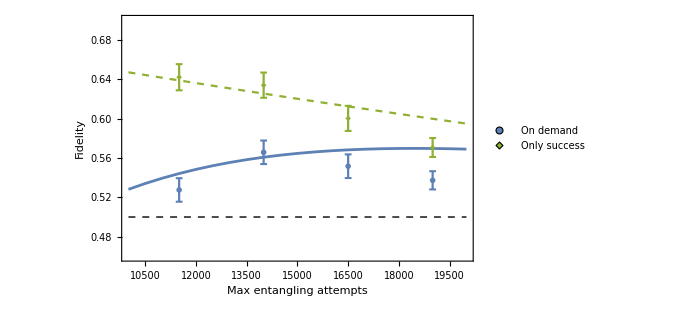
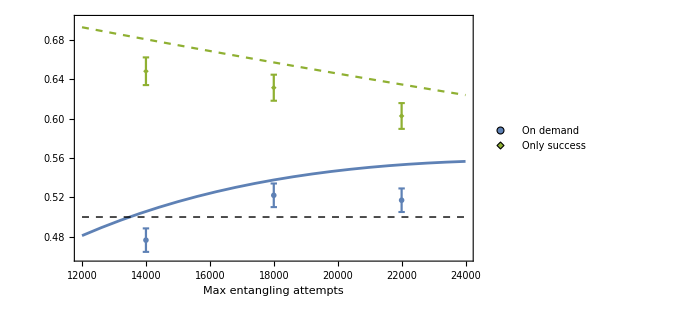

```mathematica
(* Make plots *)

modelFidPlt0p2 = ListPlot[{modelFid0p2,modelFidOnlyClicks0p2},Frame->True,FrameLabel->{"Max entangling attempts","Fidelity",Style["0.2 bright-state population",Bold],None},PlotRange->{{minPlotAttempts0p2,maxPlotAttempts0p2},{minPlotFid,maxPlotFid}},Joined->True,PlotStyle->{Directive[Thickness[0.004],col1],Directive[col2,Dashed]},Epilog->{Directive[Dashed],Line[{{minPlotAttempts0p2,0.5},{maxPlotAttempts0p2,0.5}}]}, ImageSize->500,ImagePadding->{{70,20},{50,30}}];

dataFidPlt0p2=ErrorListPlot[{dataFids0p2,dataFidsOnlyClicks0p2},PlotRange->{{minPlotAttempts0p2,maxPlotAttempts0p2},{minPlotFid,maxPlotFid}},Frame->True,FrameLabel->{"LDE Attempts","Fidelity"},PlotStyle->{Directive[PointSize[0.02],col1],Directive[PointSize[0.02],col2]},PlotMarkers->{{Graphics[{Disk[]}],0.04},{Graphics[{Polygon[{{0,1},{1,0},{0,-1},{-1,0}}]}],0.04}},PlotLegends->Placed[{"On demand","Only success"},{0.83,0.85}],ErrorBarFunction->erroBarFunc];

modelFidPlt0p15 = ListPlot[{modelFid0p15,modelFidOnlyClicks0p15},Frame->True,FrameLabel->{"Max entangling attempts","",Style["0.12 bright-state population",Bold],None},PlotRange->{{minPlotAttempts0p15,maxPlotAttempts0p15},{minPlotFid,maxPlotFid}},Joined->True,PlotStyle->{Directive[Thickness[0.004],col1],Directive[col2,Dashed]},Epilog->{Directive[Dashed],Line[{{minPlotAttempts0p15,0.5},{maxPlotAttempts0p15,0.5}}]},ImageSize->500,ImagePadding->{{40,50},{50,30}}];

dataFidPlt0p15=ErrorListPlot[{dataFids0p15,dataFidsOnlyClicks0p15},PlotRange->{{minPlotAttempts0p15,maxPlotAttempts0p15},{minPlotFid,maxPlotFid}},Frame->True,FrameLabel->{"LDE Attempts","Fidelity"},PlotMarkers->{{Graphics[{Disk[]}],0.04},{Graphics[{Polygon[{{0,1},{1,0},{0,-1},{-1,0}}]}],0.04}},PlotStyle->{Directive[PointSize[0.02],col1],Directive[PointSize[0.02],col2]},PlotLegends->Placed[{"On demand","Only success"},{0.83,0.85}],ErrorBarFunction->erroBarFunc];

Row[{Show[{modelFidPlt0p2,dataFidPlt0p2}],Show[{modelFidPlt0p15,dataFidPlt0p15}]}]
```

#### Corrs

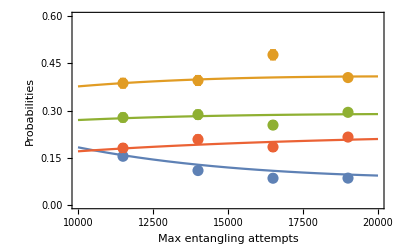
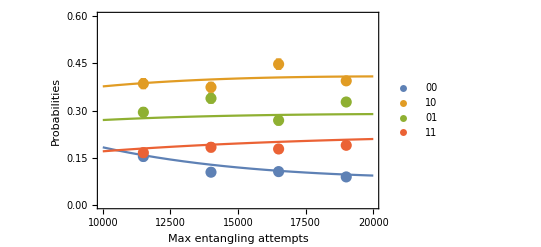

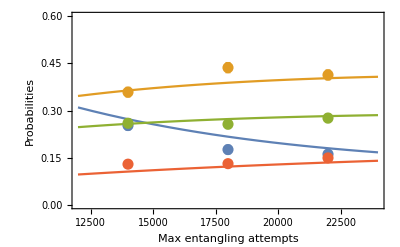
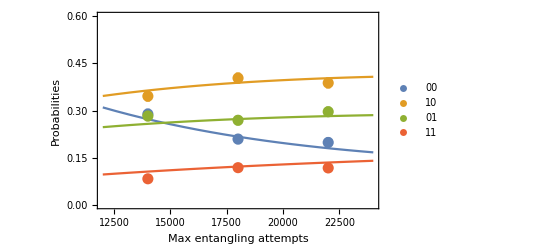

```mathematica
basis=3;
includeFails=True;

imSize = 400;

dataCorrs0p2psi0=CreateDataAvgCorrsList[LDEAttempts0p2,If[includeFails,fileCorrs0p2,fileCorrsOnlyClicks0p2],1,basis];
dataCorrsPlt0p2psi0=ErrorListPlot[dataCorrs0p2psi0,PlotStyle->{Directive[PointSize[0.02]]},ErrorBarFunction->erroBarFunc,ImageSize->imSize];

dataCorrs0p2psi1=CreateDataAvgCorrsList[LDEAttempts0p2,If[includeFails,fileCorrs0p2,fileCorrsOnlyClicks0p2],2,basis];
dataCorrsPlt0p2psi1=ErrorListPlot[dataCorrs0p2psi1,PlotStyle->{Directive[PointSize[0.02]]},ErrorBarFunction->erroBarFunc,ImageSize->imSize,PlotLegends->{"00","10","01","11"}];

dataCorrs0p15psi0=CreateDataAvgCorrsList[LDEAttempts0p15,If[includeFails,fileCorrs0p15,fileCorrsOnlyClicks0p15],1,basis];
dataCorrsPlt0p15psi0=ErrorListPlot[dataCorrs0p15psi0,PlotStyle->{Directive[PointSize[0.02]]},ErrorBarFunction->erroBarFunc,ImageSize->imSize];

dataCorrs0p15psi1=CreateDataAvgCorrsList[LDEAttempts0p15,If[includeFails,fileCorrs0p15,fileCorrsOnlyClicks0p15],2,basis];
dataCorrsPlt0p15psi1=ErrorListPlot[dataCorrs0p15psi1,PlotStyle->{Directive[PointSize[0.02]]},ErrorBarFunction->erroBarFunc,ImageSize->imSize,PlotLegends->{"00","10","01","11"}];

modelCorrs0p2psi0=ListPlot[CreatePlotLists[GetCorrs,minPlotAttempts0p2,maxPlotAttempts0p2,20,EntangleOnDemand[PopulationToTheta[0.2],#,setupParams,includeFails]&,basis,False],Frame->True,PlotRange->{{minPlotAttempts0p2,maxPlotAttempts0p2},{0,0.6}},FrameLabel->{"Max entangling attempts","Probabilities",Style["0.2 bright-state population, Psi 0",Bold],None},Joined->True,ImageSize->imSize];

modelCorrs0p2psi1=ListPlot[CreatePlotLists[GetCorrs,minPlotAttempts0p2,maxPlotAttempts0p2,20,EntangleOnDemand[PopulationToTheta[0.2],#,setupParams,includeFails,π]&,basis,False],Frame->True,PlotRange->{{minPlotAttempts0p2,maxPlotAttempts0p2},{0,0.6}},FrameLabel->{"Max entangling attempts","Probabilities",Style["0.2 bright-state population, Psi 1",Bold],None},Joined->True,ImageSize->imSize];

modelCorrs0p15psi0=ListPlot[CreatePlotLists[GetCorrs,minPlotAttempts0p15,maxPlotAttempts0p15,20,EntangleOnDemand[PopulationToTheta[0.12],#,setupParams,includeFails]&,basis,False],Frame->True,PlotRange->{{minPlotAttempts0p15,maxPlotAttempts0p15},{0,0.6}},FrameLabel->{"Max entangling attempts","Probabilities",Style["0.12 bright-state population, Psi 0",Bold],None},Joined->True,ImageSize->imSize];

modelCorrs0p15psi1=ListPlot[CreatePlotLists[GetCorrs,minPlotAttempts0p15,maxPlotAttempts0p15,20,EntangleOnDemand[PopulationToTheta[0.12],#,setupParams,includeFails,π]&,basis,False],Frame->True,PlotRange->{{minPlotAttempts0p15,maxPlotAttempts0p15},{0,0.6}},FrameLabel->{"Max entangling attempts","Probabilities",Style["0.12 bright-state population, Psi 1",Bold],None},Joined->True,ImageSize->imSize];

Row[{Show[modelCorrs0p2psi0,dataCorrsPlt0p2psi0],Show[modelCorrs0p2psi1,dataCorrsPlt0p2psi1]}]

Row[{Show[modelCorrs0p15psi0,dataCorrsPlt0p15psi0],Show[modelCorrs0p15psi1,dataCorrsPlt0p15psi1]}]
```

#### Failure rate

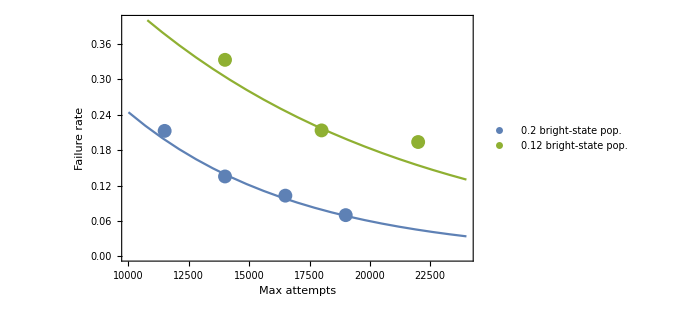

```mathematica
modelFailRate0p2=GetFailRate[0.2,minPlotAttempts0p2,maxPlotAttempts0p15,20,setupParams];
failFrac0p2=
Transpose[{LDEAttempts0p2,fileVars0p2[[#]][[2]][[3]]/Total[fileVars0p2[[#]][[2]]]&/@Range[Length[fileVars0p2]]}];

modelFailRate0p15=GetFailRate[0.12,minPlotAttempts0p2,maxPlotAttempts0p15,20,setupParams];
failFrac0p15=
Transpose[{LDEAttempts0p15,fileVars0p15[[#]][[2]][[3]]/Total[fileVars0p15[[#]][[2]]]&/@Range[Length[fileVars0p15]]}];

ListPlot[{modelFailRate0p2,failFrac0p2,modelFailRate0p15,failFrac0p15},Joined->{True,False,True,False},ImageSize->500,Frame->True,FrameLabel->{"Max attempts","Failure rate"},ImageSize->imSize,PlotStyle->{col1,Directive[PointSize[0.02],col1],col2,Directive[PointSize[0.02],col2]},PlotRange->{Automatic,{0.0,0.4}},PlotLegends->Placed[{None,"0.2 bright-state pop.",None,"0.12 bright-state pop."},{0.78,0.85}]]
```

#### Explore param space

```mathematica
(*Explore the parameterspace*)
popvsMaxAttempts[popmin_,popmax_,popsteps_,MinAttempts_,MaxAttempts_,MaxAttemptssteps_]:=Module[{},dat =Table[ FidelityEntangleOnDemand[PopulationToTheta[pop],attempts,setupParams],{attempts,MinAttempts,MaxAttempts,(MaxAttempts-MinAttempts)/MaxAttemptssteps},{pop,popmin,popmax,(popmax-popmin)/popsteps}];
ListPlot3D[ dat,AxesLabel->{"Sup. population","Maximum LDE attempts","Fidelity"},ColorFunction->"SouthwestColors",PlotLegends->Automatic,PlotTheme->"ZMesh",DataRange->{{popmin,popmax},{MinAttempts,MaxAttempts}}]];
popvsMaxAttempts[0.05,0.3,12,5000,40000,20]
```

-Graphics3D-

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

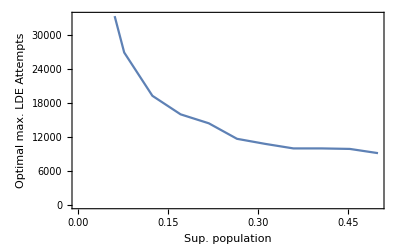

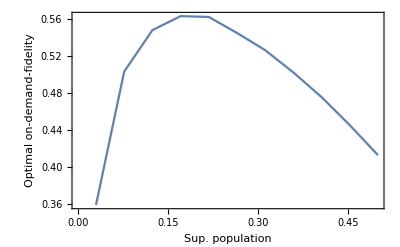

```mathematica
optimalAttemptsAndFids[popmin_,popmax_,popsteps_,ret_:False]:=Module[{attempts,dat},dat=Table[ {pop,#[[1]],attempts/.#[[2]]}&[FindMaximum[FidelityEntangleOnDemand[PopulationToTheta[pop],attempts,setupParams],{attempts,10000},AccuracyGoal->2,PrecisionGoal->2,MaxIterations->20,Method->"Newton"]],{pop,popmin,popmax,(popmax-popmin)/popsteps}];ldeAttempts=ListPlot[dat[[;;,{1,3}]],FrameLabel->{"Sup. population","Optimal max. LDE Attempts"},Frame->True,Joined->True];
fid=ListPlot[dat[[;;,{1,2}]],FrameLabel-> {"Sup. population","Optimal on-demand-fidelity"},Frame->True,Joined->True];
Print[ldeAttempts];
Print[fid];
If[ret,Return[dat]];]

optimalAttemptsAndFids[0.03,0.5,10]
```

```mathematica
(*FirstClickProbIonize[θ_,pd1_,pd2_,pdark_,attempt_]:=
FullSimplify[
Cos[θ]^4*2pdark*(1-pdark)+Sin[θ]^2 Cos[θ]^2(2pdark*(1-pdark)*(1-pd1)+2pdark*(1-pdark)*(1-pd2)+(1-pIon[attempt,θ])*(pd1*(1-pdark)^2+pd2*(1-pdark)^2))+Sin[θ]^4(2pdark*(1-pdark)*(1-pd1)*(1-pd2)+(1-pIon[attempt,θ])^2(pd2*(1-pdark)^2(1-pd1)+pd1(1-pdark)^2(1-pd2)))
]

CumProbIonize[nMax_,θ_,pd1_,pd2_,pdark_]:=(
cp = 0;
currentprod = 1;
For [i=1,i<nMax+1,i++,
(*Print[FirstClickProbIonize[θ,pd1,pd2,pdark,i]];*)
curprob = FirstClickProbIonize[θ,pd1,pd2,pdark,i];
currentprod = currentprod*(1.-curprob);
(*Print[currentprod]*)
(*p+=curprob*currentprod;*)
];
cp = 1-currentprod;
cp
)

(*First calculate the state in a way *)
CalculateRawState[θ_,Attempt_]:=(
totalattemptduration = LDEduration * Attempt;
DM = rawStateAsym[Sqrt[vis],fz,rValueAsym[θ,pDetect1,pDetect2,pDC],0];
(*include phase error due to interferometric instability*)
(*Print[pPhaseError/.t-> totalattemptduration];*)
(*Print[Tr[DM]];*)
DM = (1-pPhaseError)*DM + pPhaseError*KP[DiagonalMatrix[{1,1}],Subscript[σ, 3]].DM.(KP[DiagonalMatrix[{1,1}],Subscript[σ, 3]])†/.t-> totalattemptduration;
(*is projected into dark state based upon ionization properties*)
DM = (1-pIon[Attempt,θ])^2*DM+(1-pIon[Attempt,θ])*pIon[Attempt,θ]*(KP[Subscript[𝒫, 1],id].DM.KP[Subscript[𝒫, 1],id]†+KP[id,Subscript[𝒫, 1]].DM.KP[id,Subscript[𝒫, 1]]†)+pIon[Attempt,θ]^2 KP[Subscript[𝒫, 1],Subscript[𝒫, 1]].DM.KP[Subscript[𝒫, 1],Subscript[𝒫, 1]]† ;
(*Print[pIon[Attempt,θ]];*)
Assuming[θ>0&&Attempt>0,FullSimplify[DM]]
)


TIonization = 600000;(*1k repetitions until we ionize*)
pIon[att_,α_]:= 1-E^(-(att/TIonization)*Sin[α]^2)//N(*only population that is in ms = 0 after the θ MW-pulse will ionize*)

(*Commulative success probability. This does not include ionization*)
pltwithDC = DensityPlot[CumProb[n,θ*π,pDetect1,pDetect2,pDC],{n,1,8000},{θ,1/10,1/5},PlotLegends->Automatic,FrameLabel->{"nMax","θ (π)"},PlotLabel->"Success probability including dark counts"];
pltnoDC = DensityPlot[CumProb[n,θ*π,pDetect1,pDetect2,pDC]-CumProb[n,θ*π,pDetect1,pDetect2,0],{n,1,8000},{θ,1/10,1/5},PlotLegends->Automatic,FrameLabel->{"nMax","θ (π)"},PlotLabel->"Difference with and without dark counts"];
Grid[{{pltwithDC,pltnoDC}}]
(*These plots can also be expressed in terms of elapsed time. Can help in identifying what the metric to improve is*)
pltwithDC = DensityPlot[CumProb[n/LDEduration,θ*π,pDetect1,pDetect2,pDC],{n,1*LDEduration,8000*LDEduration},{θ,1/10,1/5},PlotLegends->Automatic,FrameLabel->{"elapsed time (ms)","θ (π)"},PlotLabel->"Success probability including dark counts"]
(*Cumulative success probability. This time with ionization!*)
pltwithDC = DensityPlot[CumProbIonize[attempts,θ*π,pDetect1,pDetect2,pDC],{attempts,1,5000},{θ,1/10,1/5},PlotLegends->Automatic,FrameLabel->{"nMax","θ (π)"},PlotLabel->"Success probability including dark counts and ionization"]
$Aborted
(Re@Fidelity[IdentityMatrix[4]/4.,bellState[2]])
0.25
*)
```